```mathematica
ClearAll["Global`*"]
```

### Define Variables

```mathematica
m=1;k=1;range={-5,5};states=3;time=20;
```

### Kinetic and Potential Energy Operator

```mathematica
T[x_]:=-Laplacian[#,{x}]/(2*m)&;
V[x_]:=0.5*k*x^2#&
```

```mathematica
H[x_]:=T[x][#]+V[x][#]&
```

### Solve the Time Independent Schrödinger Equation

```mathematica
{eigv,eigf}=NDEigensystem[{H[x][ψ[x]],DirichletCondition[ψ[x]==0,True]},ψ[x],{x,range[[1]],range[[2]]},states,
Method->{"SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.001}}}];
```

### Display the Eigenvalues of the Time Independent Schrödinger Equation

```mathematica
Transpose@{Range[states]-1,eigv}//TableForm
```

0 | 0.5
1 | 1.5
2 | 2.5

### Plot the Solutions of Time Independent Schrödinger Equation

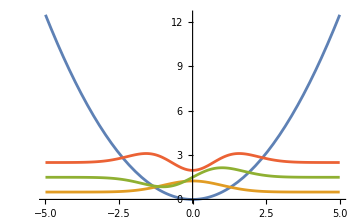

```mathematica
Plot[Evaluate@Flatten@{V[x][1],eigf+eigv},{x,range[[1]],range[[2]]},PlotRange->All]
```

### Solve the Time Dependent Schrödinger Equation

```mathematica
tdsol=ψ[x,t]/.First@#&/@NDSolve[
{I*D[ψ[x,t],{t,1}]==H[x][ψ[x,t]],ψ[x,0]==#,DirichletCondition[ψ[x,t]==0,True]},ψ[x,t],{x,range[[1]],range[[2]]},{t,0,time}
]&/@eigf;
```

### Plot the Solutions of the Time Dependent Schrödinger Equation

```mathematica
Animate[Plot[
Evaluate@Flatten@{V[x][1],#[x,t]&/@Flatten[{Function[{x,t},Re@#],Function[{x,t},Im@#]}&/@(tdsol+eigv+I*eigv)]},{x,range[[1]],range[[2]]},AxesOrigin->{0,0}
],{t,0,time},AnimationRunning->False]
```